# 38: Conjugate Gradients (CG)

We saw that Arnoldi and all sorts of other stuff became simpler for symmetric matrices. In particular, we could build a expanding orthogonal basis for the Krylov space  	
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b})
without orthogonalizing against all the previous directions.  The simplified process to build the tridiagonal H and the orthogonal Q was renamed the Lanczos process. Code to iteratively compute the diagonal α and subdiagonal β entries of H and the orthogonal Q is below.

I copied the Lanczos code below just in case

## Lanczos Code

```mathematica
LanczosInit[A_][q1_]:= Module[{v,α1,β1,q2},
v=A.q1;
α1=q1.v;
v = v - α1 q1;
β1=Norm[v];
q2=v/β1;
{{q1,q2}ᵀ,{{α1},{β1}}}
]
Lanczos[A_][{Q_,{α_,β_}}]:= Module[{m,n,qn,v,αn,βn,qNew},
{m,n}=Dimensions[Q];
qn=Q⟦All,n⟧;
v=A.qn;
αn=qn.v;
v=v-β⟦n-1⟧ Q⟦All,n-1⟧-αn qn;
βn=Norm[v];
qNew=v/βn;
{ArrayFlatten[({{Q, {qNew}ᵀ}})],{Append[α,αn],Append[β,βn]}}
]
```

Testing.  Note the preliminary initialization!

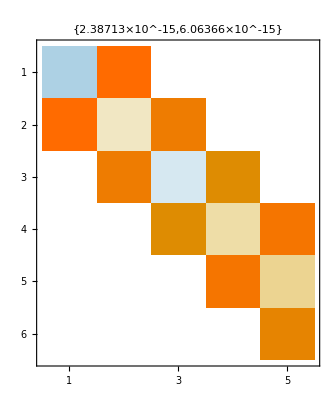

```mathematica
m=123;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
q1=Normalize[RandomReal[{-1,1},m]];
{Q1,{α1,β1}}=LanczosInit[A][q1];
n=5;
{Q,{α,β}}=Nest[Lanczos[A],{Q1,{α1,β1}},n-1];
H=SparseArray[{Band[{1,1}]->α,Band[{2,1}]->β,Band[{1,2}]->Drop[β,-1]}];
MatrixPlot[H,
PlotLabel->Map[Norm,{Qᵀ.Q-IdentityMatrix[n+1],A.Q⟦All,1;;n⟧-Q.H}]]
```

## Solving A.x=b with Conjugate Gradients.

From now on we are going to assume that A ϵ ℝ^(m×m) is Symmetric and Positive Definite abbreviated to SPD and write x_∞ for the solution satisfying A.x_∞=b.  As a reminder positive definite means x.A.x>0 unless x=0.  As a result SPD means ||x(||)_(CG(A)):=√(x.A.x) is a norm!   Minimizing the residual using this specially tailored norm gives the very simple and effective conjugate gradient algorithm.

### Residual Computation and Cost Function ϕ.

The first thing to do is to work out what is special about this way of measuring the residual.  Take a look
  	||x-x_∞(||)_(CG(A))^2=(x-x_∞).A.(x-x_∞)=(x-x_∞).(A.x-A.x_∞)=(x-x_∞).(A.x-b)=x.A.x-x.b-x_∞.A.x+x_∞.b
  Maybe nothing stand out right now but remember A=Aᵀ so x_∞.A.x=(Aᵀ.x_∞).x=(A.x_∞).x=b.x so 
  	||x-x_∞(||)_(CG(A))^2=x.A.x-x.b-x_∞.A.x+x_∞.b=x.A.x-2 x.b+x_∞.b=2(1/2 x.A.x - b.x)+constant
  The original derivation defines
  	ϕ(x)=1/2 x.A.x - b.x
  and notes that the derivative
  	Dϕ(x)=A.x - b
  is readily computable.  The factor of 2 and the constant really do not matter.  In words, we can solve A.x=b by finding the minimum of ϕ. In symbols, x_∞=argmin ϕ(x).

One way to minimize a convex function is to head straight down hill until you hit bottom in that direction and repeat the process until you get to minimum.  Straight downhill from a point x_n is the direction -Dϕ(x_n)=b-A.x_n  
which is just the residual r_n=b-A.x_n and the minimum of the single variable quadratic
	g(α):=ϕ(x_n+α r_n)=1/2((x_n+α r_n).A.(x_n+α r_n))
happens when g'(α)=-(x_n+α r_n).r_n=0 or simply
	α_n=-(x_n.r_n)/(r_n.r_n).
All we do is form our improved approximate solution x_(n+1)=x_n+α_n r_n and repeat unless Dϕ(x_(n+1))≈0.

This is a weighted steepest descent method with an "exact" line search! It is steepest descent because it searches along the negative gradient -Dϕ(x_n)!  It is an exact line search because α_n gives the true minimum along the steepest descent direction!  This means the algorithm automatically satisfies ϕ(x_(n+1))<ϕ(x_n) provided Dϕ(x_n)≠0.  In addition there is lots of geometry. Since r_n is tangent to the ϕ contour at x_(n+1) we have r_n⊥r_(n+1). Finally the g'(α)=0 condition is simply (x_n+α r_n)⊥r_n.

### Algorithm 38.1

Conjugate gradients (Algorithm 38.1) is simply this exact line search minimization starting from the predetermined  initial guess x_0=OverVector[0].  Here is the pseudo code from the text

Conjugate Gradients
x_0=0, r_0=b, p_0=r_0
for n in 1, 2, 3, ...
	α_n=(r_(n-1).r_(n-1))/(p_(n-1).A.p_(n-1))
	x_n=x_(n-1)+α_n p_(n-1)
	r_n=r_(n-1)-α_n A.p_(n-1)
	β_n=(r_n.r_n)/(r_(n-1).r_(n-1))
	p_n=r_n+β_n p_(n-1)

Conjugate Gradients
x_0=0, r_0=b, p_0=r_0
for n in 1, 2, 3, ...
	α_n=(r_(n-1).r_(n-1))/(p_(n-1).A.p_(n-1))
	x_n=x_(n-1)+α_n p_(n-1)
	r_n=r_(n-1)-α_n A.p_(n-1)
	β_n=(r_n.r_n)/(r_(n-1).r_(n-1))
	p_n=r_n+β_n p_(n-1)

Lets look at the start of this process in 2D.

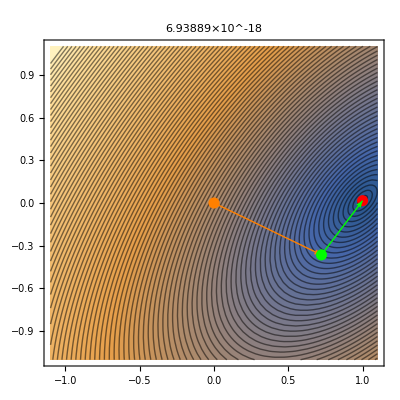

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ; 
CGNorm[A_][x_]:=√(x.A.x)
xInf= Normalize[RandomReal[{-1,1},m]];
(* Initialization *)
b=A.xInf;
r0 =b;p0=r0;x0=0*b;
α0=(r0.r0)/(p0.A.p0);
(* n=1 *)
α1 = (r0.r0)/(p0.A.p0);
x1 =x0 + α1 p0;
r1=r0-α1 A.p0;
β1 = (r1.r1)/(r0.r0);
p1=r1 + β1 p0;
(* n=2 just the start *)
α2 = (r1.r1)/(p1.A.p1);
x2 =x1 + α2 p1;
r2=r1-α2 A.p1;
(* Pic *)
ContourPlot[CGNorm[A][{x,y}-xInf],
{x,-1.1,1.1},
{y,-1.1,1.1},
Contours->100,
AspectRatio->Automatic,
Epilog->{PointSize[0.02],
{Red,Point[xInf]},
{Orange, Point[x0], Arrow[{x0,x1}]},
{Green, Point[x1], Arrow[{x1,x2}]}
},
PlotLabel->Norm[r2]
]
```

Lets try to look at the start of this process in 3D.

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ; 
CGNorm[A_][x_]:=√(x.A.x)
xInf= Normalize[RandomReal[{-1,1},m]];
(* Initialization *)
b=A.xInf;
r0 =b;p0=r0;x0=0*b;
α0=(r0.r0)/(p0.A.p0);
(* n=1 *)
α1 = (r0.r0)/(p0.A.p0);
x1 =x0 + α1 p0;
r1=r0-α1 A.p0;
β1 = (r1.r1)/(r0.r0);
p1=r1 + β1 p0;
(* n=2 just the start *)
α2 = (r1.r1)/(p1.A.p1);
x2 =x1 + α2 p1;
r2=r1-α2 A.p1;
(* Pic *)
ϕVals=Map[CGNorm[A],{x0-xInf,x1-xInf,x2-xInf}]
Show[
ContourPlot3D[CGNorm[A][{x,y,z}-xInf],
{x,-1.1,1.1},
{y,-1.1,1.1},
{z,-1.1,1.1},
ContourStyle->Opacity[0.5],
Contours->ϕVals,
AspectRatio->Automatic,
PlotLabel->Norm[r2]
],
Graphics3D[{PointSize[0.02],
{Red,Point[xInf]},
{Orange,Point[x0],Arrow[{x0,x1}]},
{Green,Point[x1],Arrow[{x1,x2}]}}]]
```

{0.729636,0.424817,0.0998797}

-Graphics3D-

### CG Code

A single step straight (the only modification is to store the matrix vector multiplication) from pseudo code.

```mathematica
CGStep[A_][{xIn_,rIn_,pIn_}]:=Module[{ApIn=A.pIn,α,β,xOut,rOut,pOut},
α=(rIn.rIn)/(pIn.ApIn);
xOut=xIn+α pIn;
rOut=rIn - α ApIn;
β = (rOut.rOut)/(rIn.rIn); 
pOut=rOut+β pIn;
{xOut,rOut,pOut}]
```

Note, all the work per step is the matrix vector-multiplication.  Find the thing that could be made more efficient! Tell me why I do not care!

Import an SPD A 
	https://math.nist.gov/MatrixMarket/data/Harwell-Boeing/bcsstruc1/bcsstk05.html
from Matrix Market.

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk05.mtx.gz"]
(*MatrixPlot[A]*)
m=Length[A];
MaxIter=22;
(* Create an identifiable RHS *)
xInf=Table[Cos[0.1 i],{i,m}];
ListPlot[xInf];
b=A.xInf;
{x0,r0,p0}={0*b, b,b};
xrpData=NestList[CGStep[A],{x0,r0,p0},MaxIter];
TabView[{
"x"->MatrixPlot[xrpData⟦All,1⟧],
"r"->MatrixPlot[xrpData⟦All,2⟧],
"p"-> MatrixPlot[xrpData⟦All,3⟧]
}]
TabView[{
"||x-x_∞(||)_(CG (A))"->ListLogPlot[Map[CGNorm[A][#-xInf]&,xrpData⟦All,1⟧]],
"||x-x_∞(||)_2"->ListLogPlot[Map[Norm[#-xInf]&,xrpData⟦All,1⟧]],
"||r||"->ListLogPlot[Map[Norm,xrpData⟦All,2⟧]]
}]
```

SparseArray[…]

123

123

Slow but very steady is the what I would say here. Remember, preconditioners are essential! We know exactly two preconditioners: Jacobi and ILU.  We are not sure if an ILU will preserve positivity but Jacobi will because the diagonal entries are positive!  In fact,almost all of them are pretty darn big!

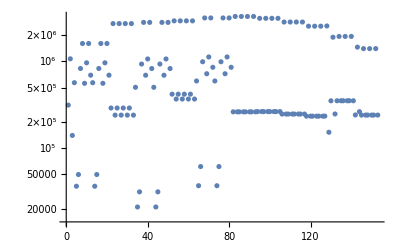

```mathematica
ListLogPlot[Diagonal[A]]
```

Lets see if we do better with A Jacobi preconditioner!  There is one serious complication: I need to make sure that the iteration matrix for CG is Symmetric!  A standard way to do this is define
	M = SparseArray[Diagonal[A]^(-1/2), {m, m}]
so that M.M is the original Jacobi preconditioner. Now solving 
	A.x=b ⟺M.A.x=M.b ⟺M.A.M.y=M.b where M.y=x
The matrix M.A.M is symmetric

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk05.mtx.gz"]
m=Length[A];
M=SparseArray[Band[{1,1}]->1/√Normal[Diagonal[A]],{m,m}];
MAM=M.A.M;
(*MatrixPlot[M.A.M];*)
MaxIter=22;
(* Create an identifiable Answer and the matching RHS *)
xInf=Table[Cos[0.1 i],{i,m}];
b=A.xInf;
Mb=M.b;
yInf=Inverse[M].xInf;
{y0,r0,p0}={0*Mb, Mb,Mb};
yrpData=NestList[CGStep[MAM],{y0,r0,p0},MaxIter];
TabView[{
"y"->MatrixPlot[yrpData⟦All,1⟧],
"r"->MatrixPlot[yrpData⟦All,2⟧],
"p"-> MatrixPlot[yrpData⟦All,3⟧]
}]
```

SparseArray[…]

123

```mathematica
TabView[{
"||y-y_∞(||)_CG"->ListLogPlot[Map[CGNorm[MAM][#-yInf]&,yrpData⟦All,1⟧],AxesLabel->{"n","||y-y_∞(||)_CG"}],
"||y-y_∞(||)_2"->ListLogPlot[Map[Norm[#-yInf]&,yrpData⟦All,1⟧],AxesLabel->{"n","||y-y_∞(||)_2"}],
"||r||"->ListLogPlot[Map[Norm,yrpData⟦All,2⟧],AxesLabel->{"n","||r||"}]
}]
```

123

Unfortunately the ILU preconditioner breaks the symmetry

```mathematica
m=Length[A];Id=SparseArray[Band[{1,1}]->1,{m,m}];
{ILU,Ipiv}=SparseArray`SparseMatrixILU[A];
{IU,IL} = {UpperTriangularize[ILU],LowerTriangularize[ILU,-1]+Id}
Hmm=IL.IU; Norm[Hmm-Hmmᵀ,"Frobenius"]
```

{SparseArray[…],SparseArray[…]}

847050.

```mathematica
SparseArray`SparseMatrixIC
```

SparseArray`SparseMatrixIC

```mathematica
Information[SparseArray`SparseMatrixIC]
```

```mathematica
Options[SparseArray`SparseMatrixILU]
```

{SparseArray`FillIn→Automatic,Method→ILUT,SparseArray`PermutationTolerance→Automatic,Tolerance→Automatic}